# Homework 8

## Exercise 1

Maximize xy such that p_xx + p_yy =w
ℒ = xy + λ(p_xx + p_yy - w)
First order condtions
(∂ℒ)/(∂x) = y + λ p_x = 0
(∂ℒ)/(∂y) = x + λ p_y = 0
(∂ℒ)/(∂λ) = p_x x + p_y y - w = 0

y + λ p_x = 0
y = -λ p_x
λ = -y/p_x

(1)	x - p_y/p_x y = 0
(2)	p_x x + p_y y = w
We can interpret (1) as the quantity of x consumed must equal the ratio of the relative price p_y/p_x times the the quantity of y consumed.

We can interpret 2 as the total amount spent  on x and y must equal wages.

(1 | -p_y/p_x
p_x | p_y) (x
y) = (0
w)

β = (1 | -p_y/p_x
p_x | p_y)
c = (0
w)

Δ = 2 p_y
β^-1 = 1/(2 p_y) (p_y | _p_y/p_x
-p_x | 1) = (1/2 | 1/(2 p_x)
-1/(2 p_x p_y) | 1/(2 p_y))
β^-1 c = (1/2 | 1/(2 p_x)
-1/(2 p_x p_y) | 1/(2 p_y)) * (0
w) = (w/(2 p_x)
w/(2 p_y))
x = w/(2 p_x) y = w/(2 p_y)
ϵ_(x, p_x) = (∂x)/(∂p_x) p_x/x = -w/(2 p_x^2) p_x/x = -w/(2 p_x)
ϵ_(x, p_y) = (∂x)/(∂p_y) p_y/y = -w/(2 p_y^2) p_y/y = -w/(2 p_y)
ϵ_(x, p_y) = (∂x)/(∂p_y) p_y/x = 0
ϵ_(y p_x) = (∂y)/(∂p_x) p_x/y = 0

```mathematica
l = x*y + λ(px*x + py*y -w)
foc1 = D[l, x] == 0
foc2 = D[l, y] == 0
foc3 = D[l, λ] ==0
reducedForm = Eliminate[{foc1, foc2, foc3},λ]
Solve[reducedForm, {x, y}]
```

x y+(-w+px x+py y) λ

y+px λ==0

x+py λ==0

-w+px x+py y==0

w==2 py y&&px x==py y

{{x→w/(2 px),y→w/(2 py)}}

## Exercise 2

Reduced Form
dQ = Q_w dw + Q_P_s dP_s
dP = P_w dw + P_s dP_s

where
F_x = (∂F)/(∂x)
Structural Form
dQ = S_P dP + S_w dw
dQ = D_P dP + D_P_s dP_s

The signs of the partial derivatives are as follows:
S_P > 0 (upward sloping supply curve)
S_w < 0 (due to increasing labor costs)
D_P< 0 (downward sloping demand curve)
D_P_s > 0 (goods are substitute

We can rewrite the above system as follows
1 dQ - Q_w dw - Q_P_S dP_s + 0 dP = 0
0 dQ - P_w dw - P_s dP_s + 1 dP = 0
1 dQ - S_w dw - 0 dP_s - S_PdP = 0
1 dQ - 0 dw - D_P_s dP_s - D_p dP = 0

(1 | -Q_w | -Q_P_s | 0
0 | -P_w | -P_s | 1
1 | -S_w | 0 | -S_P
1 | 0 | D_P_s | -D_P) (dQ
dw
dP_s
dP) = (0
0
0
0)

We can invert the coefficient matrix thusly:

```mathematica
b = {{1,-Subscript[Q, w],-Subscript[Q, Subscript[P, s]],0},{0,-Subscript[P, w],-Subscript[P, s],1},{1,-Subscript[S, w],0,-Subscript[S, P]},{1,0,Subscript[D, Subscript[P, s]],-Subscript[D, P]}}
bInv = Inverse[b]
bInv//MatrixForm
c = {{0}, {0}, {0}, {0}}
```

{{1,-Q_w,-Q_P_s,0},{0,-P_w,-P_s,1},{1,-S_w,0,-S_P},{1,0,D_P_s,-D_P}}

{{(-D_P_s P_w S_P-D_P_s S_w+D_P P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(D_P_s Q_w S_P-D_P Q_P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(P_s Q_w S_P-P_w Q_P_s S_P-Q_P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w)},{(-D_P_s+D_P P_s-P_s S_P)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(-D_P Q_P_s+D_P_s S_P+Q_P_s S_P)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(D_P_s-D_P P_s+Q_P_s)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(-Q_P_s+P_s S_P)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w)},{(-D_P P_w+P_w S_P+S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(D_P Q_w-Q_w S_P-D_P S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(D_P P_w-Q_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(Q_w-P_w S_P-S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w)},{(-D_P_s P_w+P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(D_P_s Q_w-D_P_s S_w-Q_P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(D_P_s P_w-P_s Q_w+P_w Q_P_s)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w),(P_s Q_w-P_w Q_P_s-P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w)}}

((-D_P_s P_w S_P-D_P_s S_w+D_P P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (D_P_s Q_w S_P-D_P Q_P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (P_s Q_w S_P-P_w Q_P_s S_P-Q_P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w)
(-D_P_s+D_P P_s-P_s S_P)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (-D_P Q_P_s+D_P_s S_P+Q_P_s S_P)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (D_P_s-D_P P_s+Q_P_s)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (-Q_P_s+P_s S_P)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w)
(-D_P P_w+P_w S_P+S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (D_P Q_w-Q_w S_P-D_P S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (D_P P_w-Q_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (Q_w-P_w S_P-S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w)
(-D_P_s P_w+P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (D_P_s Q_w-D_P_s S_w-Q_P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (D_P_s P_w-P_s Q_w+P_w Q_P_s)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w) | (P_s Q_w-P_w Q_P_s-P_s S_w)/(D_P_s Q_w-D_P P_s Q_w+D_P P_w Q_P_s-D_P_s P_w S_P+P_s Q_w S_P-P_w Q_P_s S_P-D_P_s S_w+D_P P_s S_w-Q_P_s S_w))

{{0},{0},{0},{0}}

```mathematica
bInv.c
```

{{0},{0},{0},{0}}

## Exercise 3

1. 
∀_(x ∈ S) (x, x) ∈ R (by reflexivity)
∀_(x, y, z ∈ S) (x, y) ∈ R ∧ (y, z) ∈ R ⇒ (x, z) ∈ R_t (by definition of transitivity)
∴ (x, x) ∈ R ∧ (x, x) ∈ R ⇒ (x, x) ∈ R_t

2. 
(x, y) ∈ R ∧ (y, x) ∈ R ⇒ (x, y) ∈ R_t (y, x) ∈ R_t (by defintion, the original relations must be in the transitive closure)
∴ R_t is symmetric

3.

## Exercise 4

For the symmetric component, we have the subset of I ⊆ R such that
{(x, x’) ∈ I} ⇔ {(x’, x) ∈ I}.  But by transitvity of R we know that (x, x’) ∈ R ∧ (x’, x’’) ∈ R ⇒ (x, x’’) ∈ R.
By symmetry we have (x’, x’’) ∈ I ⇔ (x’’, x’) ∈ I.  Therefore it must be the case that (x’, x’) ∈ I ∧ (x’, x’’) ∈ I ⇒ (x, x’’) ∈ I.

We know the original relation R is transitive, meaning 
∀_(x,y, z ∈ X)({x, y) ∈ R} ∧ ({y, z) ∈ R} ⇔ {(x, z) ∈ R}. For the asymettric component, we have the subset of R which is  {(x, x’) ∈ P} ⇒ {(x’, x) ∉ P}.  Replacing y with x’, and noting the transitive nature of the original we obtain that ∀_(x,y ∈ X)({x, x’) ∈ R} ∧ ({x’, z) ∈ R} ⇔ {(x, z) ∈ R}

By symmetry and transitivity we can replace y in the relationship 
(x P y) ∧ (y I z) to obtain (x P z). 

Similarly, by symmetry and transitivity, we can replace the second y in (x I y) ∧ (y P z) to obtain (x P z).

## Exercise 5

∀_(x, y, z ∈ S) ¬(x, y) ∈ R ∧ ¬(y, z) ∈ R ⇔ ¬(x, z)
An example of such a relationship is the “=” relationship over ℝ.
¬ (x = y) ∧ ¬ (y = z) ⇒ ¬ (x = z)
Yes. Since consumer preferences are both transitive and complete, they must also be negatively transitive.

## Exercise 6

AAC means that if ∀_(x, y ∈ y, x ≠y) x P y ⇒ ¬ y P x.  That is, if x is preferred to y then y is not preferred to x.This guarantees the existence of maximal elements. Completeness means that every pair of (x, y) can compared.  That means that maximal elements can be compared to each other to find the element that is “bigger” than all maximal elements.  So a best element must exist.

## Exercise 7

A cover C of a set S is a collection {Cn} of sets such that S ⊆ ∪C_n. That is, the set S is included in the union of the sets Cn, which may be inﬁnite in number. An open cover of S is a cover of S containing only open sets. If C and C0 each cover S, but C in smaller in the sense that C ⊂ C0, we call C a subcover from C0.
A set S ⊆ X is compact iﬀ every open cover {Cn} of S has a ﬁnite subcover {Cnk}_(k=1)^K (such that S ⊆ ∪C_n_k).

This is to say that there is a finite subcover of S.

(0, 1) is not compact. Consider [0, 1] as the smallest cover of (0, 1).  Consioder finite subsets of [0, 1] such as Cn = [0, 0.99], [0, 0.999] etc.  No finite unions ∪ Cn of these sets will give the back the set [0,1].  Thus, (0, 1) is not compact.

Consider any finite set S={x, y, z...}. By definition of cover, at least one set in C_n is S. This set is a subcover of some other set.  Therefore it is compact.

## Computational Exercise 1

The matrix representation G of a binary relation G on set S is formed by a matrix whose j^th row and k^th column is 1 iff the (j, k) ∈ G and 0 otherwise.

```mathematica
symmetricClosure[x_] := Module[{result=x}, Do[
If[result[[i]][[j]] == 1, result[[j]][[i]] =1, ],
{i, 1, Length[result]}, {j, 1, Length[result]}];
Return[result]]
```

```mathematica
reflexiveClosure[x_]:= Module[{result = x}, 
Do[
result[[i]][[i]]=1, 
{i, 1, Length[x]}];
Return[result]]

transitiveCLosure[x_] := Module[{result = x}, Return[result . result]]
```

The transitive closure is formed by squaring the original binary matrix of the relation.  The reflexive closure is formed by setting all diagonal elements to 1. The symmetricClosure is formed by checking whether (a, b) is in the oriignal relation and then adding (b, a) to the new relationship.

```mathematica
a = {{1, 1, 0}, {0, 0, 1}, {0, 0, 1}};
b = {{0, 0, 1}, {0, 1, 0}, {1, 0, 0}};
c = {{0, 0, 0}, {1, 0, 0}, {1, 1, 0}};
a//MatrixForm
b//MatrixForm
c//MatrixForm
```

(1 | 1 | 0
0 | 0 | 1
0 | 0 | 1)

(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)

(0 | 0 | 0
1 | 0 | 0
1 | 1 | 0)

xAx, xAy, yAz, zAz
xBz, yBy, zBx
yCx, zCx, zCy

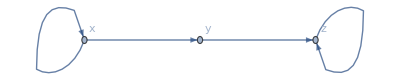
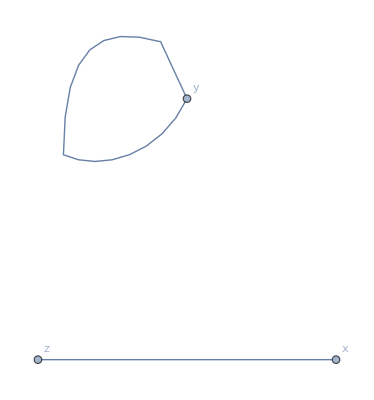
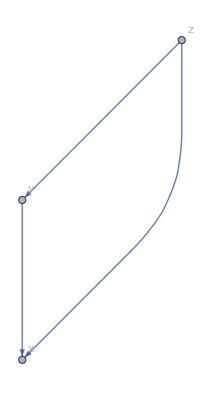

```mathematica
plotNicely = Function[x, AdjacencyGraph[x, VertexLabels->{1 -> "x", 2-> "y", 3 -> "z"}]];
Map[plotNicely, {a, b, c}]
```

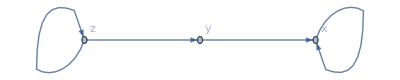
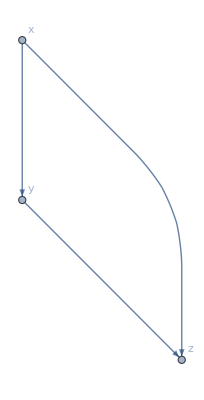
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
invA = Transpose[a ];
invB = Transpose[b];
invC = Transpose[c];
Map[plotNicely, {invA, invB, invC}]
```

{(1 | 1 | 0
1 | 0 | 1
0 | 1 | 1),(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0),(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0),(1 | 1 | 1
0 | 0 | 1
0 | 0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0),(1 | 1 | 0
0 | 1 | 1
0 | 0 | 1),(1 | 0 | 1
0 | 1 | 0
1 | 0 | 1),(1 | 0 | 0
1 | 1 | 0
1 | 1 | 1)}

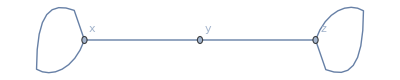
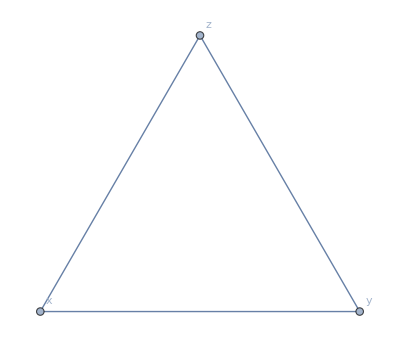
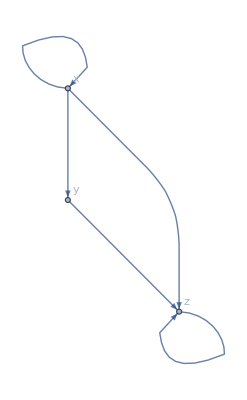
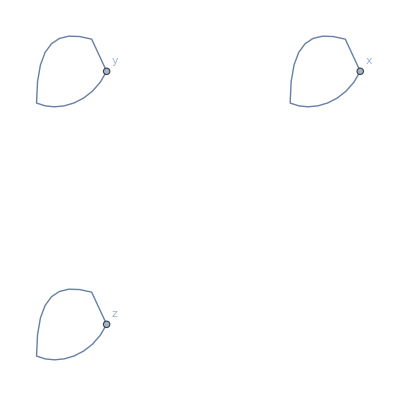
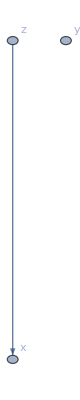
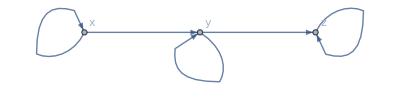
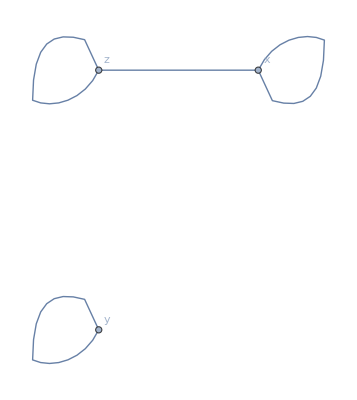
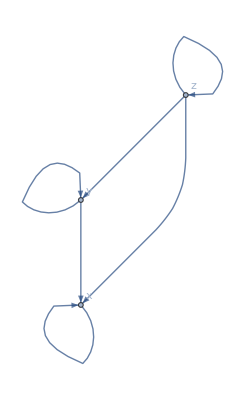
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
symA = symmetricClosure[a];
symB = symmetricClosure[b];
symC = symmetricClosure[c];
refA = reflexiveClosure[a];
refB = reflexiveClosure[b];
refC = reflexiveClosure[c];
tranA = transitiveCLosure[a];
tranB = transitiveCLosure[b];
tranC = transitiveCLosure[c];
collection = {symA, symB, symC, tranA, tranB, tranC, refA, refB, refC};
MatrixForm /@ collection
Map[plotNicely, collection]
```

## Computational Exercise 2

```mathematica
data = Table[{x, y}, {x, 1, 10}, {y, 1, 10}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10}},{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10}},{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10}},{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}}

```mathematica
MatrixForm[data]
```

((1
1) | (1
2) | (1
3) | (1
4) | (1
5) | (1
6) | (1
7) | (1
8) | (1
9) | (1
10)
(2
1) | (2
2) | (2
3) | (2
4) | (2
5) | (2
6) | (2
7) | (2
8) | (2
9) | (2
10)
(3
1) | (3
2) | (3
3) | (3
4) | (3
5) | (3
6) | (3
7) | (3
8) | (3
9) | (3
10)
(4
1) | (4
2) | (4
3) | (4
4) | (4
5) | (4
6) | (4
7) | (4
8) | (4
9) | (4
10)
(5
1) | (5
2) | (5
3) | (5
4) | (5
5) | (5
6) | (5
7) | (5
8) | (5
9) | (5
10)
(6
1) | (6
2) | (6
3) | (6
4) | (6
5) | (6
6) | (6
7) | (6
8) | (6
9) | (6
10)
(7
1) | (7
2) | (7
3) | (7
4) | (7
5) | (7
6) | (7
7) | (7
8) | (7
9) | (7
10)
(8
1) | (8
2) | (8
3) | (8
4) | (8
5) | (8
6) | (8
7) | (8
8) | (8
9) | (8
10)
(9
1) | (9
2) | (9
3) | (9
4) | (9
5) | (9
6) | (9
7) | (9
8) | (9
9) | (9
10)
(10
1) | (10
2) | (10
3) | (10
4) | (10
5) | (10
6) | (10
7) | (10
8) | (10
9) | (10
10))

```mathematica
u[{x_, y_}] := Return[x*y]
```

```mathematica
util = Table[u[{x, y}], {x, 1, 10}, {y, 1, 10}]
```

{{1,2,3,4,5,6,7,8,9,10},{2,4,6,8,10,12,14,16,18,20},{3,6,9,12,15,18,21,24,27,30},{4,8,12,16,20,24,28,32,36,40},{5,10,15,20,25,30,35,40,45,50},{6,12,18,24,30,36,42,48,54,60},{7,14,21,28,35,42,49,56,63,70},{8,16,24,32,40,48,56,64,72,80},{9,18,27,36,45,54,63,72,81,90},{10,20,30,40,50,60,70,80,90,100}}

```mathematica
util//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100)

```mathematica
equivalentClass[{j_, k_}] :=  Position[util, j*k]
```

```mathematica
equivalentClass[{6, 5}]
```

{{3,10},{5,6},{6,5},{10,3}}

```mathematica
getLower[{j_, k_}] := Position[util, _? (# < j*k)&]
```